```mathematica
SizedDots[n_]:= Table[ Directive[PointSize[0.05*(n+1-i)/n],Hue[i/n]],{i,n}]
```

# Henon Map

## Basic Map and Attractor

The Henon map has simple derivatives etc.

```mathematica
F[a_,b_][{x_,y_}]:={1- a x^2 + y, b x}
DF[a_,b_][{x_,y_}]:={{-2 a x,1},{b,0}}
```

Our target is to start to understand how the structure of the attractor develops as we change a and b.  In particular we are going to see if it looks different for parmaeter values different from the default 	
	{a,b}={1.4,0.3}.

## Parametric Dependence: Visual Exploration.

Lets try to get a feel for what it does. It is hard to see what happens in the Phase Space

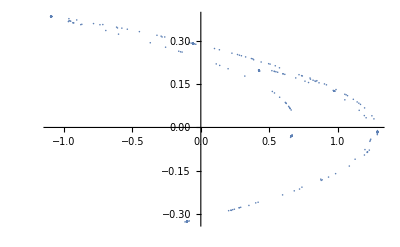

```mathematica
MaxIter=12345;
{a,b}={1.25,0.3};
Data=NestWhileList[F[a,b],{0.21,0.3},Norm[#]<10&,1,MaxIter]⟦10;;-1⟧;
ListPlot[Data]
```

It may easier to see what is going on with “time” included.

```mathematica
MaxIter=1234;
{a,b}={1.23,0.3};
Data=NestWhileList[F[a,b],{0.21,0.3},Norm[#]<10&,1,MaxIter];TabView[{
"x_1"->ListPlot[ Data⟦All,1⟧,AxesLabel->{"k","x_1"}],
"x_2"->ListPlot[ Data⟦All,2⟧,AxesLabel->{"k","x_2"}]
}]
```

12

## Parametric Dependence: Orbit/Bifurcation Diagram.

Lets try to see what happens as we change a.

```mathematica
MaxIter=1234;
b=0.3;
{aMin,aMax,da}={0.8,1.3,0.005};
BigData=Table[
Data=NestWhileList[F[a,b],{0.21,0.3},Norm[#]<10&,1,MaxIter],
{a,aMin,aMax,da}];
Dimensions[BigData]
```

{101,1235,2}

We now have a bunch of {x_1,x_2} values which we need to split up and associate with the appropriate values of a.

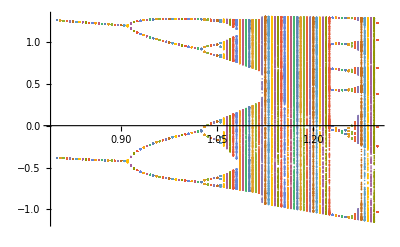

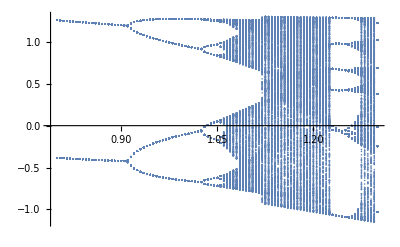

```mathematica
Clear[a]
a[i_]:= aMin+(i-1) da
x1Data=Table[
Map[{a[i],#}&,BigData⟦i,200;;-1,1⟧],
{i,1,Length[BigData]}];
ListPlot[x1Data]
ListPlot[Partition[Flatten[x1Data],2],PlotRange->All]
```

## Periodic Point Computations

### Development and Planning From Class on Nov 8.

Here is a random (well not so random but we can change it) starting point getting stuck on the attractor

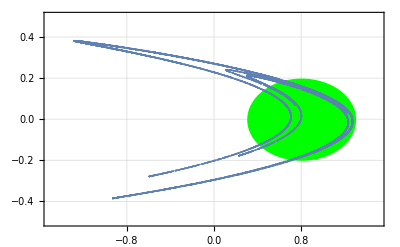

```mathematica
MaxIter=12345;
{a,b}={1.4,0.3};
Data=NestList[F[a,b],{0.21,0.3},MaxIter]⟦10;;MaxIter⟧;
Pic=ListPlot[Data,
Prolog->{Green,Disk[{0.8,0},{0.5,0.2}]},
GridLines->Automatic,
Frame->True,
PlotRange->{{-1.5,1.5},{-0.5,0.5}}
]
```

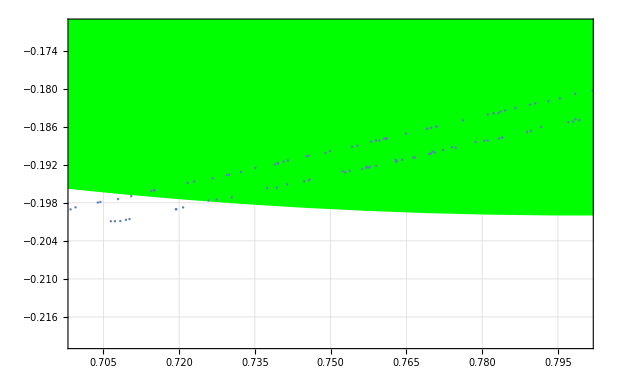

```mathematica
Show[
Pic, PlotRange->{{0.7,0.8},{-0.22,-0.17}}]
```

I want to compute a bunch of periodic points and plot them.   This can not be algebraic for say p>4 so it needs to be numeric and I want to choose reasonable random initial conditions.  The easiest way to do this is to construct a simple region that encloses the dots.

It is easy enough to grab a bunch of random points (Initial Conditions) from a region and throw them into the periodic point solver.

```mathematica
SampleSize=124;
ICs=RandomPoint[Disk[{0.8,0},{0.5,0.2}],SampleSize];
p=6;
Clear[G]
G[p_][xy_]:=Nest[F[a,b],xy,p]-xy
FPs=Union[Quiet[Table[
xy/.FindRoot[ G[p][xy]==0,{xy,IC}],
{IC,ICs}]],
SameTest->(Norm[#1-#2]≤10^-6&)];
(* Eliminate the bad guys *)
FPs={FPs,Map[Norm,Map[G[p],FPs]]}ᵀ;
FPs=Select[FPs, #⟦2⟧<10^-8&]⟦All,1⟧
```

{{0.44191,-0.241266},{0.485336,0.132573},{0.579544,-0.218328},{0.631354,0.189406},{0.802802,0.145601},{0.9758,-0.14274},{1.03806,0.0934357},{1.07012,-0.124548},{1.15796,0.0729942}}

```mathematica
#>2&]
```

```mathematica
?Select
```

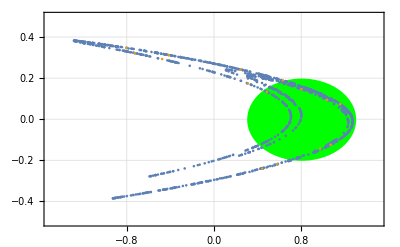

```mathematica
FPs = FPs;
FPs=Union[Partition[Flatten[Map[NestList[F[a,b],#,p-1]&, FPs]],2],
SameTest->(Norm[#1-#2]≤10^-6&)];
ListPlot[{Data,FPs},
Prolog->{Green,Disk[{0.8,0},{0.5,0.2}]},
GridLines->Automatic,
Frame->True,
PlotRange->{{-1.5,1.5},{-0.5,0.5}}
]
```

All we need to do is get rid of duplicates and maybe tidy up a bit.   We should also make a function so that when we fix something it stays fixed.

### Code

The plan is to find period p orbits for the Henon map with parameters a and b by running FindRoot on s points chosen randomly from a region.  It returns the successful solutions.

```mathematica
HenonPeriodic[{a_,b_},p_,{sampleSize_, myRegion_}]:= Module[
{ICs,F,x,y,G,xy,FPs,AllTol=10^-8},
(* Draw Random ICs *)
ICs = RandomPoint[myRegion,sampleSize];
(* Define Functions *)
F[{x_,y_}]:={1- a x^2 + y, b x};
G[xy_]:=Nest[F,xy,p]-xy;
(* Run FindRoot on ICs *)
(* Compute and store points and residuals then purge non converged entries *)
FPs=Quiet[Table[
{xy,Norm[G[xy]]}/.FindRoot[ G[xy]==0,{xy,IC}],
{IC,ICs}]];
(* Eliminate non-converged entries and ditch residudals *)
FPs=Select[FPs, #⟦2⟧<AllTol&]⟦All,1⟧;
(* Purge Duplicates *)
FPs =Union[FPs,SameTest->(Norm[#1-#2]≤AllTol&)];
(* Build the orbits *) 
FPs = Map[NestList[F,#,p-1]&, FPs];
(* Rearrange to a list of periodic points *)
FPs=Partition[Flatten[FPs],2];
(* Purge Duplicates and return *)
FPs =Union[FPs,SameTest->(Norm[#1-#2]≤AllTol&)]
]
```

We need to test this!

```mathematica
{MaxIter,sampleSize}={1234,300};
{a,b}={1.4,0.3};
Data=NestList[F[a,b],{0.21,0.3},MaxIter]⟦10;;MaxIter⟧;
myRegion=Polygon[
{{-1.3817613275913452,0.44320135130398675},{1.4176440068799847,0.19974141018989555},{1.4176440068799847,-0.14974141180590173},{-1.330796861164039,-0.4815537540378665},{-1.3125952660114297,-0.23220365070378635},{0.47480137797481614,-0.02801144009950063},{0.3510305309370718,0.11335239801115926},{-1.3926822846829112,0.31754460861544476}}];
pMax=13;
Do[
PeriodicPoints[p]=HenonPeriodic[{a,b},p,{sampleSize, myRegion}],
{p,1,pMax}];
```

```mathematica
{MaxIter,sampleSize}={1234,500};
{a,b}={1.4,0.3};
Data=NestList[F[a,b],{0.21,0.3},MaxIter]⟦10;;MaxIter⟧;
myRegion=Polygon[
{{-1.3817613275913452,0.44320135130398675},{1.4176440068799847,0.19974141018989555},{1.4176440068799847,-0.14974141180590173},{-1.330796861164039,-0.4815537540378665},{-1.3125952660114297,-0.23220365070378635},{0.47480137797481614,-0.02801144009950063},{0.3510305309370718,0.11335239801115926},{-1.3926822846829112,0.31754460861544476}}];
pMax=13;
Do[
PeriodicPoints[p]=HenonPeriodic[{a,b},p,{sampleSize, myRegion}],
{p,13,15}];
```

Lets see what they look like.

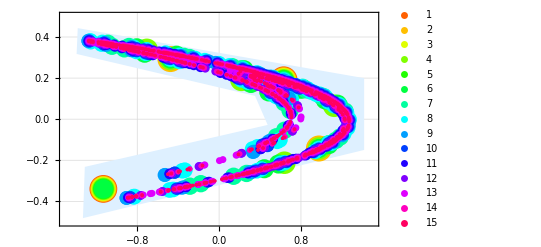

```mathematica
Pic=ListPlot[
Table[PeriodicPoints[p],{p,1,15}],
PlotStyle->SizedDots[16],
Prolog->{LightBlue,myRegion},
GridLines->Automatic,
Frame->True,
PlotLegends->Table[p,{p,1,15}],
PlotRange->{{-1.5,1.5},{-0.5,0.5}}
]
```

Looks good to me.

```mathematica
TableForm[Table[Length[PeriodicPoints[p]],{p,1,15}],
TableHeadings->Automatic,
TableDirections->Row]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
2 | 4 | 2 | 8 | 2 | 16 | 29 | 63 | 55 | 102 | 155 | 246 | 416 | 630 | 1050

```mathematica
416/13
```

32

## Break

Lets look at them on top of the attractor.

```mathematica
ColoredDots[n_]:= Table[
Directive[PointSize[0.05 (1-0.8 i/n)],Hue[i/n]],{i,1, n}]
```

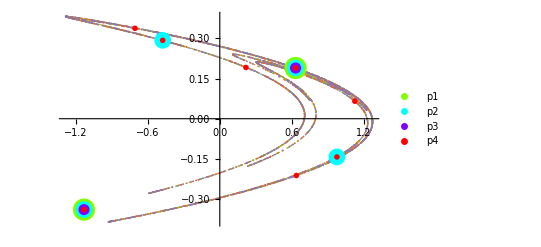

```mathematica
Show[Pic,
ListPlot[{p1,p2,p3,p4},
PlotLegends->{"p1","p2","p3","p4"},
PlotStyle->ColoredDots[4]
]]
```

We can find higher period solutions we just can not guarantee to find all of them.  The following builds the equations for the a periodic point of period p then runs Newton’s method with a single initial condition. Remember Newtons method does not always converge nicely!

```mathematica
{a,b}={1.4,0.3};
p=10;
G[p][{x_,y_}]:= Nest[F[a,b],{x,y},p]-{x,y}
xy[p] ={x,y}/.FindRoot[G[p][{x,y}],{{x,0.4},{y,0.5}}]
G[p][xy[p]]
```

{-0.868789,-0.380348}

{9.80216×10^-12,8.72136×10^-13}

{0.243314,0.240841}

{-7.77156×10^-16,1.11022×10^-16}

```mathematica
{a,b}={1.4,0.3};
p=7;
G[p][{x_,y_}]:= Nest[F[a,b],{x,y},p]-{x,y}
xy[p] ={x,y}/.FindRoot[G[p][{x,y}],{{x,0.1},{y,0.1}}];
G[p][xy[p]]
```

{3.9968×10^-15,-5.27356×10^-16}

```mathematica
{a,b}={1.4,0.3};
p=8;
G[p][{x_,y_}]:= Nest[F[a,b],{x,y},p]-{x,y}
xy[p] ={x,y}/.FindRoot[G[p][{x,y}],{{x,0.1},{y,0.1}}];
G[p][xy[p]]
```

{-3.21965×10^-15,4.16334×10^-16}

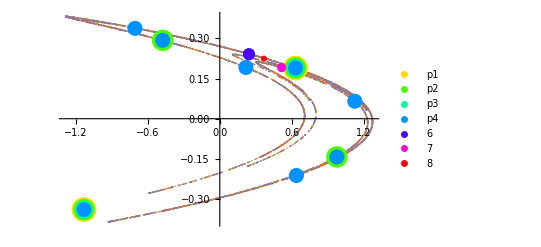

```mathematica
Show[Pic,
ListPlot[{p1,p2,p3,p4,{xy[6]},{xy[7]},{xy[8]}},
PlotLegends->{"p1","p2","p3","p4","6","7","8"},
PlotStyle->ColoredDots[7]
]]
```

Each of the high order cycles we found is a representative of a number of the orbit. For instance!

```mathematica
NestList[F[a,b],xy[8],8-1]
```

{{0.90003,0.131886},{-0.00218859,0.270009},{1.27,-0.000656578},{-1.25872,0.381001},{-0.837142,-0.377617},{-0.358746,-0.251143},{0.568679,-0.107624},{0.439622,0.170604}}

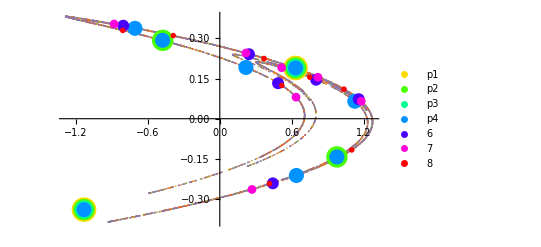

```mathematica
Show[Pic,
ListPlot[{p1,p2,p3,p4,
NestList[F[a,b],xy[6],6-1],
NestList[F[a,b],xy[7],7-1],
NestList[F[a,b],xy[8],8-1]},
PlotLegends->{"p1","p2","p3","p4","6","7","8"},
PlotStyle->ColoredDots[7]
]]
```

To convince you that there are lots of periodic points.

{-1.33257×10^-11,-3.50686×10^-12}

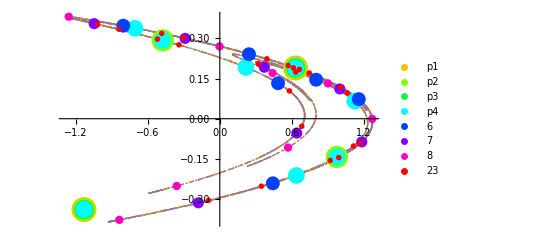

```mathematica
{a,b}={1.4,0.3};
p=23;
G[p][{x_,y_}]:= Nest[F[a,b],{x,y},p]-{x,y}
xy[p] ={x,y}/.FindRoot[G[p][{x,y}],{{x,0.1},{y,0.1}}];
G[p][xy[p]]
Show[Pic,
ListPlot[{p1,p2,p3,p4,
NestList[F[a,b],xy[6],6-1],
NestList[F[a,b],xy[7],7-1],
NestList[F[a,b],xy[8],8-1],
NestList[F[a,b],xy[23],23-1]},
PlotLegends->{"p1","p2","p3","p4","6","7","8","23"},
PlotStyle->ColoredDots[8]
]]
```

There is no reason to think that there is only one 23 cycle! There could be, but there is no reason to think that.  Lets go look for another couple

{-5.11552×10^-12,-4.91995×10^-13}

{-5.30886×10^-12,6.5839×10^-13}

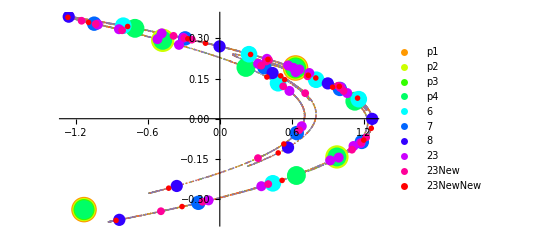

```mathematica
{a,b}={1.4,0.3};
p=23;
G[p][{x_,y_}]:= Nest[F[a,b],{x,y},p]-{x,y}
Newxy[p] ={x,y}/.FindRoot[G[p][{x,y}],{{x,0.2},{y,0.1}}];
NewNewxy[p] ={x,y}/.FindRoot[G[p][{x,y}],{{x,0.2},{y,0.2}}];
G[p][Newxy[p]]
G[p][NewNewxy[p]]
Show[Pic,
ListPlot[{p1,p2,p3,p4,
NestList[F[a,b],xy[6],6-1],
NestList[F[a,b],xy[7],7-1],
NestList[F[a,b],xy[8],8-1],
NestList[F[a,b],xy[23],23-1],
NestList[F[a,b],Newxy[23],23-1],
NestList[F[a,b],NewNewxy[23],23-1]},
PlotLegends->{"p1","p2","p3","p4","6","7","8","23","23New","23NewNew"},
PlotStyle->ColoredDots[10]
]]
```

Lets go and see how the 23 cycles we found are joined up.

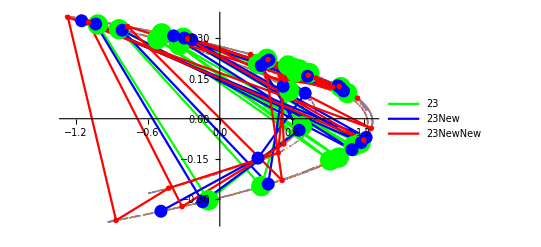

```mathematica
Show[Pic,
ListPlot[{
NestList[F[a,b],xy[23],23-1],
NestList[F[a,b],Newxy[23],23-1],
NestList[F[a,b],NewNewxy[23],23-1]},
PlotLegends->{"23","23New","23NewNew"},
PlotStyle->ColoredDots[3],
Joined->True,
Mesh->All
]]
```

We should take from this that there are lots of periodic orbits with lots of different periods!

## Jacobians for Periodic Orbits

A periodic orbit is convenient because it comes right back where it started!  We are going to look at the period 6 orbit we found.

{x→0.243314,y→0.240841}

{{0.243314,0.240841},{1.15796,0.0729942},{-0.80422,0.347387},{0.44191,-0.241266},{0.485336,0.132573},{0.802802,0.145601}}

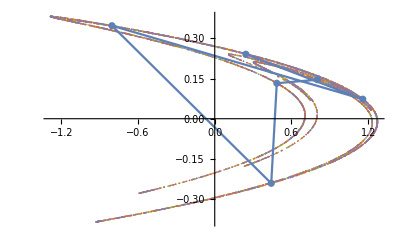

```mathematica
{a,b}={1.4,0.3};
p=6;
G[p][{x_,y_}]:= Nest[F[a,b],{x,y},p]-{x,y}
xySub = FindRoot[G[p][{x,y}],{{x,0.1},{y,0.1}}]
xy[p] ={x,y}/.xySub;
orbit[p]=NestList[F[a,b],xy[p],p-1]
Show[Pic, ListPlot[orbit[p],Joined->True,Mesh->All]]
```

Since 6 is not to big I can compute the Jacobian of the nested map! and evaluate it at the

```mathematica
Clear[J6]
p=6;
J6[{x_,y_}]=D[Nest[F[a,b],{x,y},p],{{x,y}}];
orbit[p]=NestList[F[a,b],xy[p],p-1];
J6Matrices= Map[J6,orbit[p]]
Map[SingularValueList, J6Matrices]
```

{{{-23.7496,30.5188},{2.93002,-3.76517}},{{-24.557,7.93315},{9.15563,-2.95776}},{{-28.6793,-14.0335},{2.37994,1.16454}},{{-30.4362,21.1211},{-4.21004,2.92152}},{{-23.2127,15.7602},{6.33634,-4.30208}},{{-25.7193,9.76672},{4.72806,-1.79548}}}

{{38.9641,0.0000187095},{27.5418,0.0000264688},{32.0384,0.0000227539},{37.3996,0.0000194922},{29.0838,0.0000250655},{27.9723,0.0000260615}}

The round trip singular values are not the same at all the points but they are all seriously distorted by roughly the same amount.  A typical value is ~30/0.000025≈1.2 10^6.

There is another way to compute these nested derivatives.  It is called the chain rule! All we have to do is evaluate the gradient at each point in the orbit and the multiply them together in the appropriate order. That order is backwards!

```mathematica
JMatrices =Map[DF[a,b],orbit[p]];
Apply[Dot,Reverse[JMatrices]]
J6Matrices⟦1⟧
```

{{-23.7496,30.5188},{2.93002,-3.76517}}

{{-23.7496,30.5188},{2.93002,-3.76517}}

To get the others I need to start at a different point. i.e I rotate the matrices.

```mathematica
Apply[Dot, RotateRight[Reverse[JMatrices],1]]
J6Matrices⟦2⟧
```

{{-24.557,7.93315},{9.15563,-2.95776}}

{{-24.557,7.93315},{9.15563,-2.95776}}

```mathematica
Apply[Dot, RotateRight[Reverse[JMatrices],2]]
J6Matrices⟦3⟧
```

{{-28.6793,-14.0335},{2.37994,1.16454}}

{{-28.6793,-14.0335},{2.37994,1.16454}}

## Jacobian Pics (start)

I am still going to look at the period six orbit we found and plot out the images of a circle as it goes round the orbit.

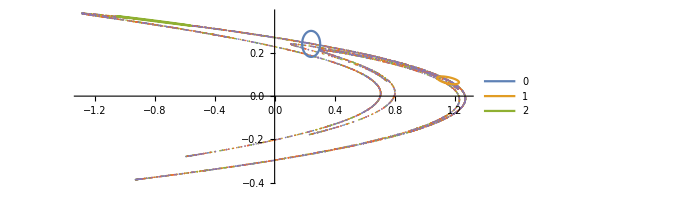

```mathematica
Clear[J6]
p=6;
J6[{x_,y_}]=D[Nest[F[a,b],{x,y},p],{{x,y}}];
orbit[p]=NestList[F[a,b],xy[p],p-1];
r=0.06;
Show[Pic,
ParametricPlot[ {
orbit[p]⟦1⟧+r {Cos[θ],Sin[θ]},
F[a,b][orbit[p]⟦1⟧+r {Cos[θ],Sin[θ]}],
Nest[F[a,b],orbit[p]⟦1⟧+r {Cos[θ],Sin[θ]},2]
},{θ,0, 2π},
PlotLegends->{0,1,2,3,4,5,6}],
AspectRatio->Automatic
]
```

## Curves and Dots

I want to have some idea where the attractor is and what it looks like up close.

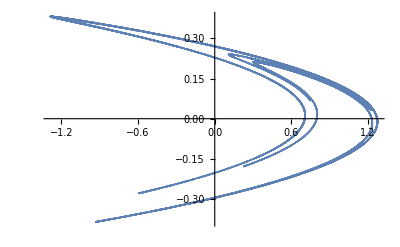

```mathematica
MaxIter=32345; {x0,y0}={0.1,0.2};
Data=NestList[F[a,b],{x0,y0},MaxIter]⟦20;;-1⟧;
Pic=ListPlot[Data]
Show[Pic, PlotRange->{{0,0.2},{0.25,0.3}}];
```

Here is a more convenient way to zoom in.

```mathematica
ZoomBounds={
{{0,0.1},{0.2,0.3}},
{{0.6,0.85},{-0.1,0.1}},
{{1.1,1.3},{0,0.1}}
};
atlas=Show[Pic,
Prolog->Table[
{{xMin,xMax},{yMin,yMax}}=ZoomBounds⟦i⟧;
{
{EdgeForm[Thin],Hue[i/Length[ZoomBounds]], Opacity[0.2],Rectangle[{xMin,yMin},{xMax,yMax}]},
Text[i,0.5({xMin,yMin}+{xMax,yMax})]},
{i,1,Length[ZoomBounds]}]];
TabView[
Join[{"atlas"->atlas},
Table[
i->Show[atlas,PlotRange->ZoomBounds[[i]]],{i,Length[ZoomBounds]}]
]
]
```

1234

## Decomposition and Animation

The map F is the composition of three simpler things: a bend 
	{x,y}->{x,1-a x^2+y};
a scaling in the x-direction
	{x,y}->{ b x, y}
followed by the flip
	{x,y}→{y,x}. 
All but the middle one preserve areas.  Easy enough to check

```mathematica
Clear[a,b]
Bend[a_,tb_][{x_,y_}]:={x,y+tb*(1- a x^2)}
HScale[b_,ts_][{x_,y_}]:={((1-ts)+ts*b)*x,y}
Flip[tf_][{x_,y_}]:={(1-tf)*x + tf*y,(1-tf)*y+tf*x}
Flip[1][HScale[b,1][Bend[a,1][{x,y}]]]
```

{1-a x^2+y,b x}

Inspired by the wiki page 
	https://en.wikipedia.org/wiki/H%C3%A9non_map
here is an animation doing it once.

```mathematica
{a,b}={1.4,0.3};
NumSamples=1000;
ps=RandomReal[{-2,2},{NumSamples,2}];
Bps=Map[Bend[a,1],ps];
SBps=Map[HScale[b,1],Bps];
SetOptions[Animate,
AnimationRunning->False,
AnimationRepetitions->1];
TabView[{
"Bend"->Animate[ListPlot[Map[Bend[a,tb],ps],
PlotRange->{{-2,2},{-2,2}},
AspectRatio->Automatic],
{tb,0,1}],
"Scale"->Animate[ListPlot[Map[HScale[b,th],Bps],
PlotRange->{{-2,2},{-2,2}},
AspectRatio->Automatic],
{th,0,1}],
"Flip"->Animate[ListPlot[Map[Flip[tf],SBps],
PlotRange->{{-2,2},{-2,2}},
AspectRatio->Automatic],
{tf,0,1}]
}]
```

123

Here is an animation doing it more than once a

```mathematica
{a,b}={1.4,0.3};
NumSamples=2000;
ps=RandomReal[{-2,2},{NumSamples,2}];
SubSteps=10; MaxIter=9;
Ps=ps;
ListAnimate[Apply[Join,Table[
Join[
Table[
ListPlot[Map[Bend[a,tb],Ps],
PlotRange->{{-2,2},{-2,2}},
PlotLabel->StringForm["Iteration ``: Bend a=``",i, a,i],
AspectRatio->Automatic],
{tb,1/SubSteps,1,1/SubSteps}],
Ps=Map[Bend[a,1],Ps];
Table[
ListPlot[Map[HScale[b,ts],Ps],
PlotRange->{{-2,2},{-2,2}},
PlotLabel->StringForm["Iteration ``: Scale b=``",i,b],
AspectRatio->Automatic],
{ts,1/SubSteps,1,1/SubSteps}],
TempPs=Map[HScale[b,1],Ps];
Ps=Map[Flip[1],TempPs];
Table[
ListPlot[Map[Flip[tf],TempPs],
PlotRange->{{-2,2},{-2,2}},
PlotLabel->StringForm["Iteration = ``: Flip",i],
AspectRatio->Automatic],
{tf,1/SubSteps,1,1/SubSteps}]
],
{i,1,MaxIter}]],
AnimationRunning->False,
AnimationRate->0.1]
```

```mathematica
Animate
```

Animate

```mathematica
Bend[a_,t1_][{x_,y_}]:={x, t*(1-a
```

```mathematica
Clear[a,b]
F[a,b][{x,y}]
```

{1-a x^2+y,b x}

I want to have some idea where the attractor is and what it looks like up close.

```mathematica
MaxIter=32345; {x0,y0}={0.1,0.2};
Data=NestList[F[a,b],{x0,y0},MaxIter]⟦20;;-1⟧;
Pic=ListPlot[Data]
Show[Pic, PlotRange->{{0,0.2},{0.25,0.3}}];
```

-Graphics-

Here is a more convenient way to zoom in.

```mathematica
ZoomBounds={
{{0,0.1},{0.2,0.3}},
{{0.6,0.85},{-0.1,0.1}},
{{1.1,1.3},{0,0.1}}
};
atlas=Show[Pic,
Prolog->Table[
{{xMin,xMax},{yMin,yMax}}=ZoomBounds⟦i⟧;
{
{EdgeForm[Thin],Hue[i/Length[ZoomBounds]], Opacity[0.2],Rectangle[{xMin,yMin},{xMax,yMax}]},
Text[i,0.5({xMin,yMin}+{xMax,yMax})]},
{i,1,Length[ZoomBounds]}]];
TabView[
Join[{"atlas"->atlas},
Table[
i->Show[atlas,PlotRange->ZoomBounds[[i]]],{i,Length[ZoomBounds]}]
]
]
```

1234

## Mapped Area goes to zero Fast

At each iteration any region of area A is mapped to a region with area A*b.  So if I keep mapping it and do it  n times then an initial region of area A_0 is mapped to a region of area b^n A_0.

Lets make sure we understand this.  The map and the Jacobian matrix (derivative are) is

```mathematica
F[a_,b_][{x_,y_}]:={1-a x^2+y,b x}
J[a_,b_][{x_,y_}]:= {{-2 a x,1},{b,0}}
```

The determinant of the Jacobian is -b so from calc II we know that areas are multiplied by |b|.  So we know the attractor has dimension less than 2 provided b<1.

## Crude Replication Count

How many disks of radius α σ_2 does it take to cover an ellipse with major axis σ_1 and minor axis σ_2<σ_1.

I think it is easier to think of arranging n uniformly disks along the major axis of the thin ellipse

### Odd Number of Identical Disks: Middle Disk Centered

If there are an odd number of disks the center disk should be centered in the ellipse.   The distance from the middle of the ellipse to the x-coordinate of the intersection point with the ellipse is.

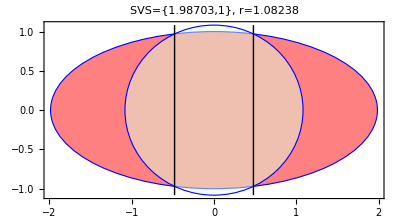

```mathematica
Clear[r,ϵ]
{x,y}/.Solve[ {x^2+y^2==r^2, ϵ^2 x^2+y^2==1}, {x,y}];
OddxInt[r_,e_]:= √((r^2-1)/(1-e^2))
e=RandomReal[{0.1,0.9}];
σ2=1; σ1=σ2/e;
r=RandomReal[{σ2,σ1}];
β =OddxInt[r,e];
Graphics[{EdgeForm[Blue],
{Pink,Disk[{0,0},{σ1,σ2}]},
{LightGreen,Opacity[0.5],Disk[{0,0},r]},
{Line[{{-β,-r},{-β,r}}],Line[{{β,-r},{β,r}}]}
},
AspectRatio->Automatic,
PlotLabel->StringForm["SVS=``, r=``",{σ1,σ2},r],
Frame->True]
```

I think it is more convenient to think of the required radius as a function of the offset and eccentricity.  This is easy enough to do by hand 
	β=√((r^2-1)/(1-e^2)) ⟹ β^2=(r^2-1)/(1-e^2) ⟹ β^2(1-e^2)=r^2-1 ⟹ r^2=1+β^2(1-e^2) ⟹ r=√(1+β^2(1-e^2))

Looks as though it is doing the right thing I do need to understand the 2 I added.

1.02529

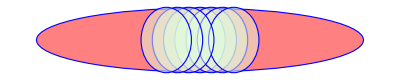

```mathematica
Oddr[β_,e_]:=Sqrt[1+β^2(1-e^2)]
 e=RandomReal[{0.05,0.2}];
σ2=1; σ1=σ2/e;
β =RandomReal[{0.1 σ2,σ2}];
rMin=Oddr[β,e]
Graphics[{EdgeForm[Blue],
{Pink,Disk[{0,0},{σ1,σ2}]},
{LightGreen,Opacity[0.5],
Disk[{0,0},rMin],
Disk[{2β,0},rMin],
Disk[{4β,0},rMin],
Disk[{6β,0},rMin],
Disk[{-2β,0},rMin],
Disk[{-4β,0},rMin],
Disk[{-6β,0},rMin]}}]
```

Now what I need to do is work out how to pick the number of Disks!

I know the eccentricity.

I need to make the number of disks, radius of Disks, and resulting offset cover the major axis of the ellipse.

It is length 1/e!

I need something to be bigger than 1/e.  It is an integer multiple of the offset plus the radius

I need to think about n*r^d for whatever I think d might be!

According to Wikipedia  d = 1.261 ± 0.003

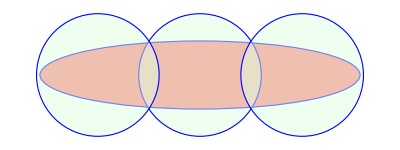

```mathematica
{σ1,σ2}={4.7,1};
α=1.8;β=3;
Graphics[{EdgeForm[Blue],
{Pink,Disk[{0,0},{σ1,σ2}]},
{LightGreen,Opacity[0.5],Disk[{0,0},α σ2],Disk[{β,0},α σ2],Disk[{-β,0},α σ2]}}]
```

```mathematica
3*
```